# Probabilistics of Hardy's Scheme

Nicholas Wheeler
Reed College Physics Department
11 May 2010

### Introduction

Bohm, Bell and later Hardy all contemplate situations in which Alice & Bob do measurements on their respective components of a composite pair of 2-state systems. The scheme—drawn on the presumption that Alice makes the first measurement, Bob the second—is illustrated below:

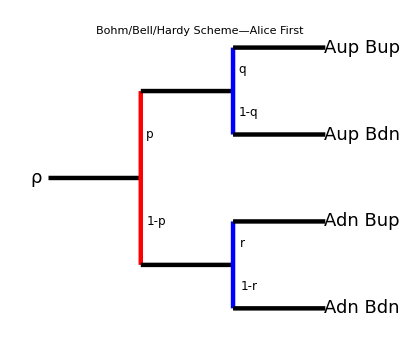

```mathematica
Show[Graphics[{Thickness[0.008],Line[{{0,0},{1,0}}]}],
Graphics[{Red,Thickness[0.008],Line[{{1,-1},{1,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,+1},{2,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,-1},{2,-1}}]}],
Graphics[{Blue,Thickness[0.008],Line[{{2,1/2},{2,3/2}}]}],
Graphics[{Blue,Thickness[0.008],Line[{{2,-1/2},{2,-3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,3/2},{3,3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,1/2},{3,1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-1/2},{3,-1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-3/2},{3,-3/2}}]}],
Graphics[Text[Style["p", FontSize->12],{1.1,0.5}]],
Graphics[Text[Style["1-p", FontSize->12],{1.17,-0.5}]],
Graphics[Text[Style["q", FontSize->12],{2.1,1.25}]],
Graphics[Text[Style["1-q", FontSize->12],{2.17,.75}]],
Graphics[Text[Style["r", FontSize->12],{2.1,-.75}]],
Graphics[Text[Style["1-r", FontSize->12],{2.17,-1.25}]],Graphics[Text[Style["Aup Bup", FontSize->18],{3.4,1.50}]],
Graphics[Text[Style["Aup Bdn", FontSize->18],{3.4,0.50}]],
Graphics[Text[Style["Adn Bup", FontSize->18],{3.4,-0.50}]],
Graphics[Text[Style["Adn Bdn", FontSize->18],{3.4,-1.50}]],
Graphics[Text[Style["ρ", FontSize->18],{-0.13,0}]],
PlotLabel->Style["Bohm/Bell/Hardy Scheme—Alice First", Blue, FontFamily->"Helvetica", FontSize->14]]
```

```mathematica
Clear[p,q,r,P]
```

Alice's results are, in effect, marginal probabilities—independent of the results of Bob's subsequent results:

```mathematica
Subscript[P, Aup]=p;
Subscript[P, Adn]=1-p;
```

Bob's results are conditional probabilites, contingent upon the results of Alice's prior measurement:

```mathematica
Subscript[P, Bup,Aup]=q;
Subscript[P, Bdn,Aup]=1-q;
Subscript[P, Bup,Adn]=r;
Subscript[P, Bdn,Adn]=1-r;
```

REMARK: The preferred notation here would be P_(Bup|Aup), which Mathematica disallows. Whence the comma.

Joint probabilities are obtained by appeal to the formula

joint=conditional*marginal

```mathematica
Subscript[P, AupBup]=Subscript[P, Bup,Aup] Subscript[P, Aup]
Subscript[P, AupBdn]=Subscript[P, Bdn,Aup] Subscript[P, Aup]
Subscript[P, AdnBup]=Subscript[P, Bup,Adn] Subscript[P, Adn]
Subscript[P, AdnBdn]=Subscript[P, Bdn,Adn] Subscript[P, Adn]
```

p q

p (1-q)

(1-p) r

(1-p) (1-r)

These sum to unity:

```mathematica
Subscript[P, AupBup]+Subscript[P, AupBdn]+Subscript[P, AdnBup]+Subscript[P, AdnBdn]//Simplify
```

1

From the joint probabilities we can recover Alice's marginal probabilities

```mathematica
Subscript[P, Aup]=Subscript[P, AupBup]+Subscript[P, AupBdn]//Simplify
Subscript[P, Adn]=Subscript[P, AdnBup]+Subscript[P, AdnBdn]//Simplify
```

p

1-p

and can—if we assume the joint probabilities are independent of the sequence in which Alice/Bob make their measurements (Bohm/Bell/Hardy contemplate situations in which it would be relativistically impossible to assign covariant meaning to such a sequence)—assign marginal probabilities also to Bob:

```mathematica
Subscript[P, Bup]=Subscript[P, AupBup]+Subscript[P, AdnBup]
Subscript[P, Bdn]=Subscript[P, AupBdn]+Subscript[P, AdnBdn]
```

p q+(1-p) r

p (1-q)+(1-p) (1-r)

```mathematica
Subscript[P, Bdn]==1-Subscript[P, Bup]//Simplify
```

True

```mathematica
Subscript[P, Aup,Bup]=Subscript[P, AupBup]/Subscript[P, Bup]
Subscript[P, Aup,Bdn]=Subscript[P, AupBdn]/Subscript[P, Bdn]
Subscript[P, Adn,Bup]=Subscript[P, AdnBup]/Subscript[P, Bup]
Subscript[P, Adn,Bdn]=Subscript[P, AdnBdn]/Subscript[P, Bdn]
```

(p q)/(p q+(1-p) r)

(p (1-q))/(p (1-q)+(1-p) (1-r))

((1-p) r)/(p q+(1-p) r)

((1-p) (1-r))/(p (1-q)+(1-p) (1-r))

We are in position now to construct the scheme that arises when it is Bob who makes the first measurement:

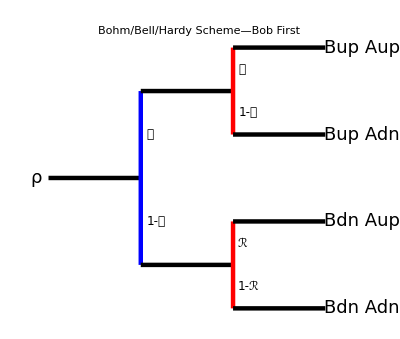

```mathematica
Show[Graphics[{Thickness[0.008],Line[{{0,0},{1,0}}]}],
Graphics[{Blue,Thickness[0.008],Line[{{1,-1},{1,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,+1},{2,+1}}]}],
Graphics[{Thickness[0.008],Line[{{1,-1},{2,-1}}]}],
Graphics[{Red,Thickness[0.008],Line[{{2,1/2},{2,3/2}}]}],
Graphics[{Red,Thickness[0.008],Line[{{2,-1/2},{2,-3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,3/2},{3,3/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,1/2},{3,1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-1/2},{3,-1/2}}]}],
Graphics[{Thickness[0.008],Line[{{2,-3/2},{3,-3/2}}]}],
Graphics[Text[Style["𝒫", FontSize->12],{1.1,0.5}]],
Graphics[Text[Style["1-𝒫", FontSize->12],{1.17,-0.5}]],
Graphics[Text[Style["𝒬", FontSize->12],{2.1,1.25}]],
Graphics[Text[Style["1-𝒬", FontSize->12],{2.17,.75}]],
Graphics[Text[Style["ℛ", FontSize->12],{2.1,-.75}]],
Graphics[Text[Style["1-ℛ", FontSize->12],{2.17,-1.25}]],Graphics[Text[Style["Bup Aup", FontSize->18],{3.4,1.50}]],
Graphics[Text[Style["Bup Adn", FontSize->18],{3.4,0.50}]],
Graphics[Text[Style["Bdn Aup", FontSize->18],{3.4,-0.50}]],
Graphics[Text[Style["Bdn Adn", FontSize->18],{3.4,-1.50}]],
Graphics[Text[Style["ρ", FontSize->18],{-0.13,0}]],
PlotLabel->Style["Bohm/Bell/Hardy Scheme—Bob First", Blue, FontFamily->"Helvetica", FontSize->14]]
```

NOTE that the logic of the diagram has led us to place BupAdn=AdnBup where AupBdn formerly resided; ditto BdnAup=AupBdn  where AdnBup formerly resided.

We can now describe Bob's {𝒫, 𝒬, ℛ} in terms of Alice's {p, q, r}

```mathematica
𝒫=p q+(1-p) r;
𝒬=(p q)/(p q+(1-p) r);
ℛ=(p (1-q))/(p (1-q)+(1-p) (1-r));
```

and could similarly describe Alice's {p, q, r} in terms of Bob's {𝒫, 𝒬, ℛ}.

The joint probabilities that result from Bob's scheme

```mathematica
𝒫 𝒬
𝒫(1-𝒬)//Simplify
(1-𝒫)ℛ//Simplify
(1-𝒫)(1-ℛ)//Simplify
```

p q

r-p r

p-p q

(-1+p) (-1+r)

differ only by the previously noted permutation from those that have been found to result from Alice's scheme:

```mathematica
Subscript[P, AupBup]
Subscript[P, AupBdn]//Simplify
Subscript[P, AdnBup]//Simplify
Subscript[P, AdnBdn]//Simplify
```

p q

p-p q

r-p r

(-1+p) (-1+r)

### Hardy's 𝕌𝕌 arrangement

Hardy imposes the condition P_AupBup= 0. To achieve that without at the same time forcing P_AupBdn= 0 we set

```mathematica
q=0;
```

The joint probabilities become

```mathematica
Subscript[P, AupBup]
Subscript[P, AupBdn]
Subscript[P, AdnBup]
Subscript[P, AdnBdn]
```

0

p

(1-p) r

(1-p) (1-r)

More interesting are the marginal probabilities

```mathematica
Subscript[P, Bup,Aup]
Subscript[P, Bdn,Aup]
Subscript[P, Bup,Adn]
Subscript[P, Bdn,Adn]
```

0

1

r

1-r

```mathematica
Subscript[P, Bup]=Subscript[P, AupBup]+Subscript[P, AdnBup];
Subscript[P, Bdn]=Subscript[P, AupBdn]+Subscript[P, AdnBdn];

Subscript[P, Aup,Bup]=Subscript[P, AupBup]/Subscript[P, Bup]
Subscript[P, Aup,Bdn]=Subscript[P, AupBdn]/Subscript[P, Bdn]
Subscript[P, Adn,Bup]=Subscript[P, AdnBup]/Subscript[P, Bup]
Subscript[P, Adn,Bdn]=Subscript[P, AdnBdn]/Subscript[P, Bdn]
```

0

p/(p+(1-p) (1-r))

1

((1-p) (1-r))/(p+(1-p) (1-r))

Specifically, from

```mathematica
Subscript[P, Bup,Aup]
Subscript[P, Bdn,Aup]

Subscript[P, Aup,Bup]
Subscript[P, Adn,Bup]
```

0

1

0

1

we see that if one gets "up" the other gets "dn"